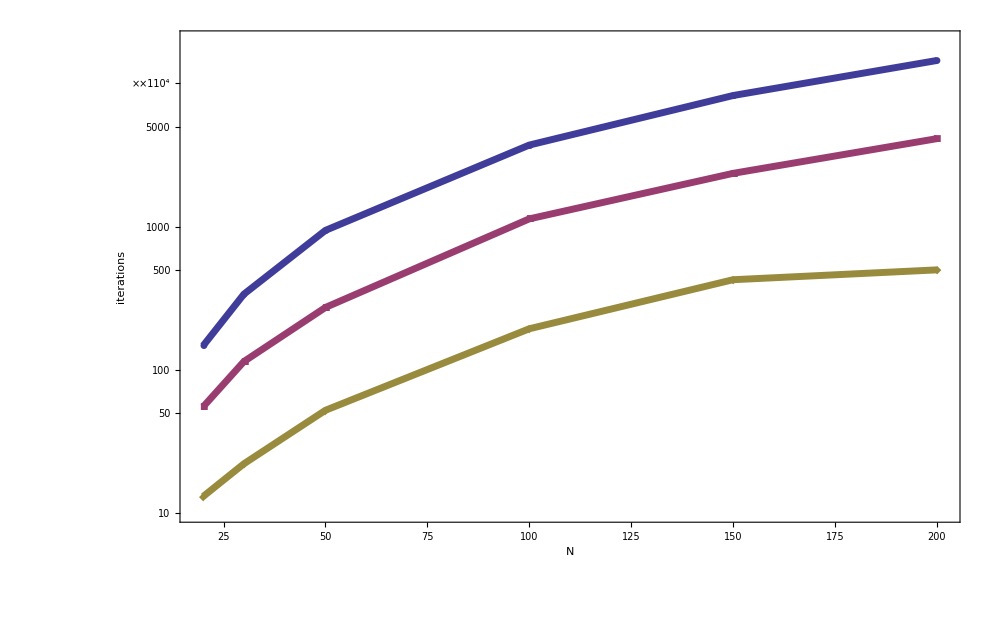

```mathematica
(*1_1*)
NN={20,30,50,100, 150, 200};
(*NN=10.^-#&/@NN;*)

sp={147,337,940,3709,8230, 14463};
spopress={55,114,272,1131,2353, 4112};
spcond={13,22,52,193, 425, 498};
Needs["PlotLegends`"]
gp[NN_,arr_]:=Partition[Riffle[NN,arr],2];
g1=ListLogPlot[{gp[NN, sp], gp[NN,spopress], gp[NN,spcond]},LabelStyle->Directive[Bold,FontSize->20,Black],Frame->True,PlotMarkers->Automatic ,Joined->True,PlotStyle->{{Directive[PointSize[.4]],Thickness[0.005]}},Axes->False,PlotLegendStyle->{Large},PlotLegend->{Style["SP",20,Bold],Style["SP OPRESS",20,Bold],Style["SP PRECOND",20,Bold]},LegendPosition->{1.1,-0.4},Joined->{True,True,False},PlotMarkers->Automatic,FrameLabel->{"N","iterations"},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->1000, PlotRange->{{18,202},{10,20000}}]
Export["E:\\university\\diploma\\docs\\tex\\pics\\num_ex_2_2_1.pdf",g1];
```

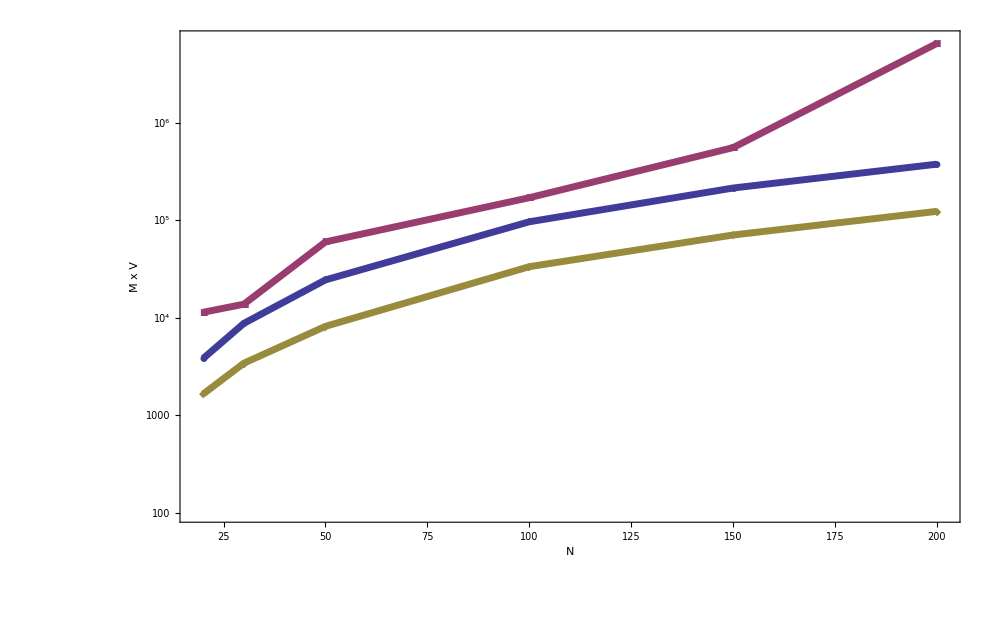

```mathematica
sp={3823,8763,24441,96435,213981, 376039};
spopress={1651,3421,8161,33391,70591, 123361};
spcond={11373,13779,59949,170268, 555381, 6505863};
g2=ListLogPlot[{gp[NN, sp],gp[NN,spcond], gp[NN,spopress]},LabelStyle->Directive[Bold,FontSize->20,Black],Frame->True,PlotMarkers->Automatic ,Joined->True,PlotStyle->{{Directive[PointSize[.4]],Thickness[0.005]}},Axes->False,PlotLegendStyle->{Large},PlotLegend->{Style["SP",20,Bold],Style["SP PRECOND",20,Bold], Style["SP OPRESS",20,Bold]},LegendPosition->{1.1,-0.4},Joined->{True,True,False},PlotMarkers->Automatic,FrameLabel->{"N","M x V"},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->1000, PlotRange->{{18,202},{100,7000000}}]
Export["E:\\university\\diploma\\docs\\tex\\pics\\num_ex_2_2_2.pdf",g1];
```

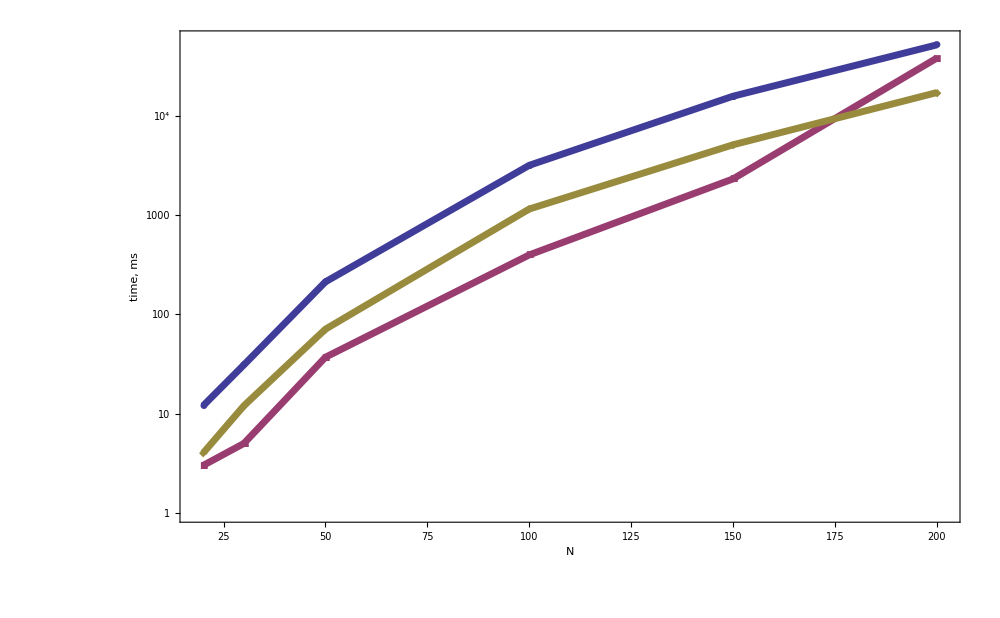

{20,30,50,100,150,200}

```mathematica
sp={12, 31, 213,3186,15857,52229};
spopress={4, 12,71,1155,5133,17251};
spcond={3,5,37,398,2324,38410};
g2=ListLogPlot[{gp[NN, sp],gp[NN,spcond], gp[NN,spopress]},LabelStyle->Directive[Bold,FontSize->20,Black],Frame->True,PlotMarkers->Automatic ,Joined->True,PlotStyle->{{Directive[PointSize[.4]],Thickness[0.005]}},Axes->False,PlotLegendStyle->{Large},PlotLegend->{Style["SP",20,Bold],Style["SP PRECOND",20,Bold], Style["SP OPRESS",20,Bold]},LegendPosition->{1.1,-0.4},Joined->{True,True,False},PlotMarkers->Automatic,FrameLabel->{"N","time, ms"},FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},ImageSize->1000, PlotRange->{{18,202}, {1,58000}}]
Export["E:\\university\\diploma\\docs\\tex\\pics\\num_ex_2_2_3.pdf",g1];
NN//ScientificForm
```

```mathematica
Options[ListPlot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,InterpolationOrder→None,Joined→False,LabelStyle→{},MaxPlotPoints→∞,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotMarkers→None,PlotRange→Automatic,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,Ticks→Automatic,TicksStyle→{}}

```mathematica
10^10
```

10000000000